```mathematica
Clear["Global`*"]
ClearSystemCache[]
```

## Set Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Load in Suave

```mathematica
Install["Suave-Linux"];
Install["Vegas-Linux"];
Install["Divonne-Linux"];
```

## Global Constants

```mathematica
TEMP = ((1.*^3/1.16*^4 )*1.*^-9); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
hbarc = (0.1973269788*1.*^-3); (* GeV fm *)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = Transpose[{radius,nb*Yn}];
nd          = Interpolation[ndList]; (* Neutron density in fm^-1*)

ndFreeList =(2.*NM*muList)^1.5/(3.*π^2*hbarc^3);

ndCorrectedList = (ndList*ndList)/ndFreeList;

ndCorrected = Interpolation[Transpose[{radius, ndCorrectedList}]]

NSMass = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

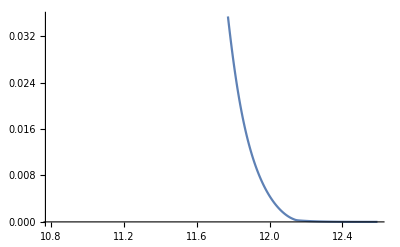

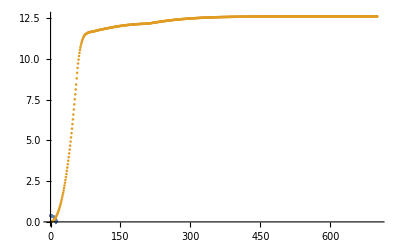

{3.85096×10^13,3.85095×10^13,3.85092×10^13,3.85087×10^13,3.85076×10^13,3.85057×10^13,3.85027×10^13,3.84981×10^13,3.84914×10^13,3.84821×10^13,3.84695×10^13,3.84528×10^13,3.8431×10^13,3.84033×10^13,3.83684×10^13,3.83252×10^13,3.82724×10^13,3.82083×10^13,3.81316×10^13,3.80404×10^13,3.79329×10^13,3.78071×10^13,3.7661×10^13,3.74924×10^13,3.72989×10^13,3.70782×10^13,3.68277×10^13,3.6545×10^13,3.62273×10^13,3.58721×10^13,3.54767×10^13,3.50385×10^13,3.45548×10^13,3.40231×10^13,3.34409×10^13,3.28061×10^13,3.21166×10^13,3.13704×10^13,3.05659×10^13,2.9702×10^13,2.87777×10^13,2.77924×10^13,2.6746×10^13,2.56387×10^13,2.44713×10^13,2.32449×10^13,2.19608×10^13,2.06206×10^13,1.92256×10^13,1.77765×10^13,1.63094×10^13,1.48706×10^13,1.347×10^13,1.21172×10^13,1.08206×10^13,9.21772×10^12,7.84945×10^12,6.68265×10^12,5.68884×10^12,4.84345×10^12,4.12533×10^12,3.51627×10^12,3.00061×10^12,2.56491×10^12,2.1976×10^12,1.88875×10^12,1.62982×10^12,1.41341×10^12,1.23311×10^12,1.08331×10^12,9.59084×10^11,8.5611×10^11,7.70608×10^11,7.19371×10^11,6.79193×10^11,6.459×10^11,6.17233×10^11,5.91751×10^11,5.6835×10^11,5.45771×10^11,5.18511×10^11,5.02452×10^11,4.8977×10^11,4.78306×10^11,4.67886×10^11,4.89475×10^11,4.69352×10^11,4.54785×10^11,4.40048×10^11,4.30748×10^11,4.20536×10^11,4.12424×10^11,4.05018×10^11,3.975×10^11,3.89482×10^11,3.78801×10^11,3.68566×10^11,3.58723×10^11,3.49231×10^11,3.40057×10^11,3.31174×10^11,3.22555×10^11,3.14176×10^11,3.06016×10^11,2.98059×10^11,2.90287×10^11,2.82686×10^11,2.75245×10^11,2.67954×10^11,2.60802×10^11,2.53784×10^11,2.46892×10^11,2.40121×10^11,2.33468×10^11,2.26927×10^11,2.20497×10^11,2.14175×10^11,2.0796×10^11,2.01851×10^11,1.95846×10^11,1.89945×10^11,1.84149×10^11,1.78456×10^11,1.72867×10^11,1.67383×10^11,1.62003×10^11,1.56728×10^11,1.51558×10^11,1.46494×10^11,1.41537×10^11,1.36685×10^11,1.31941×10^11,1.27303×10^11,1.22772×10^11,1.18348×10^11,1.14031×10^11,1.09821×10^11,1.05717×10^11,1.01718×10^11,9.78252×10^10,9.40366×10^10,9.03518×10^10,8.67699×10^10,8.32899×10^10,7.99107×10^10,7.6631×10^10,7.34496×10^10,7.03652×10^10,6.73762×10^10,6.44813×10^10,6.16786×10^10,5.89667×10^10,5.63439×10^10,5.38083×10^10,5.13582×10^10,4.89918×10^10,4.67073×10^10,4.45027×10^10,4.23761×10^10,4.03258×10^10,3.83497×10^10,3.6446×10^10,3.46128×10^10,3.28481×10^10,3.11501×10^10,2.95169×10^10,2.79467×10^10,2.64376×10^10,2.49878×10^10,2.35956×10^10,2.22592×10^10,2.09768×10^10,1.97468×10^10,1.85675×10^10,1.74373×10^10,1.63546×10^10,1.53179×10^10,1.43256×10^10,1.33762×10^10,1.24682×10^10,1.16004×10^10,1.07712×10^10,9.97933×10^9,9.22343×10^9,8.50221×10^9,7.81438×10^9,7.15872×10^9,6.534×10^9,5.93904×10^9,5.37272×10^9,4.83397×10^9,4.32184×10^9,3.83554×10^9,3.37457×10^9,2.9388×10^9,2.63754×10^9,2.34749×10^9,2.06958×10^9,1.82545×10^9,1.61902×10^9,1.4367×10^9,1.26778×10^9,1.10471×10^9,9.40116×10^8,7.58994×10^8,4.95741×10^8,3.42789×10^8,1.98567×10^8,5.70632×10^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListLinePlot[Transpose[{radius,nb*Yn}]]
```

## Useful Functions

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*NSMass[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*NSMass[rMax]*2.*^30)/(rMax*1.*^3)]/SOL
]; 


EscVel = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];


FermiDirac[s_, t_, vel_ , chempot_,dm_]:= Module[                               (* vel can be to be interchanged for initial and final velocities *)
{MU, MUP, argument},
MU = dm/NM;
MUP = (MU+1.)/2.;
argument = (1/TEMP(0.5*NM*(2.*MU*MUP*t^2.*MUP*s^2-MU*vel^2) - chempot));
Which[(argument > 700.), 0., argument<-700., 1., True,
	1./(1. + Exp[argument])]
]; 

PreFacs[dm_]:= Module[
{MU, MUP},
(MU = dm/NM;
MUP = (MU + 1.)/2.;
 64*π*MUP^4*Erf[((Sqrt[(3/2)]*NSVEL)/VELDISP)]*1.*^54)/(NSVEL*dm)
];
```

## Define Integrand

```mathematica
OmegaIntegrand[s_, t_, v_, w_, chempot_, dm_ ] := Module[
{},

Which[(w - Abs[s - t]<0), 0, (s+t -w <0),0, (v - Abs[s - t]<0), 0, (s+t -v <0),0, True,
v*t*FermiDirac[s, t, w, chempot, dm]*(1. - FermiDirac[s, t, v, chempot, dm])
]
];
```

## Do the integrals

```mathematica
dCdV[r_,dm_] := Module[
{w, chempot, FVSqr, MU, MUP, tbound, sbound},

MU = dm/NM;
MUP = (MU + 1.)/2.;

w             =EscVel[r];
chempot = muFn[r]*1.*^-3;
FVSqr = (2.*chempot)/NM;

tbound =3.*Sqrt[(FVSqr + MU*w^2)/(2*MU * MUP)];
sbound = 3.*Sqrt[(FVSqr + MU*w^2)/(2*MUP)];

{sbound, tbound, Divonne[OmegaIntegrand[s, t, v,w, chempot, dm], {v, 0, EscVel[r]}, {s, 0, sbound}, {t, 0, tbound},AccuracyGoal->4, MaxPoints->1000000, Verbose->0]}
];
```

```mathematica
CperV = Interpolation[Table[{x,dCdV[x, 1.*^-3][[1]]},{x, rMin, 12, ((12-rMin)/(100-1))}]]
```

Divonne::success: Needed 23820 integrand evaluations on 194 subregions.

General::stop: Further output of Divonne::success will be suppressed during this calculation.

InterpolatingFunction[{{0.0045726, 12.}}, <>]

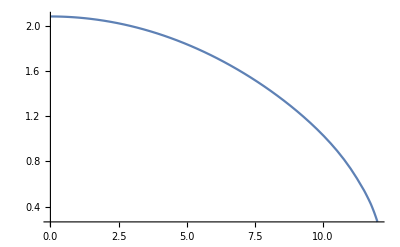

```mathematica
Plot[CperV[x], {x, rMin, 12}]
```

## Integrating over semi-infinite domain example

```mathematica
(*
f[tx_, ty_, dm_] := Module[{x, y, jacobian},
x = tx/(1-tx);
y = ty/(1-ty);
jacobian = 1/(1-tx)^2*1/(1-ty)^2;
Exp[-x^2-y^2]*jacobian*dm
];
*)
```